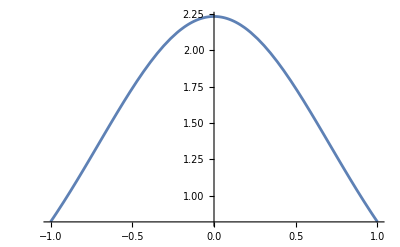

```mathematica
Plot[NIntegrate[Exp[-x^2- y^2-z^2], {x,-1,1}, {y,-1,1}], {z,-1,1}]
```

```mathematica
NIntegrate[Exp[-x^2- y^2-z^2], {x,-1,1}, {y,-1,1}, {z,0,1}]
```

1.66615

```mathematica
ϵ = 10^-3;
NIntegrate[1/(2 ϵ)Exp[-x^2- y^2-z^2], {x,-1,1}, {y,-1,1}, {z,-ϵ,ϵ}]

NIntegrate[Exp[-x^2- y^2], {x,-1,1}, {y,-1,1}]
```

2.23098

2.23099

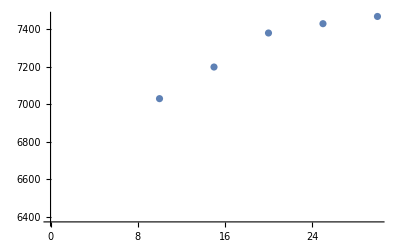

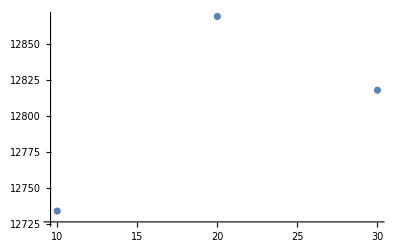

```mathematica
dat = {
{5, 5824.843825564134},
{10, 7030.835732926975}, 
{15, 7199.449262813205},
{20, 7380.826826793514},
{25, 7430.525305313924},
 {30, 7469.060645004771}};
adat = {
{5, 13538.923577698026},
{10, 12733.708944613509}, 
{15, 12801.41917253457},
{20, 12869.069022823489}, 
{25, 12855.11263519752},
{30, 12817.78607865313
}};

ListPlot[{dat}]
```

```mathematica
(84.0 - 16.1)
```

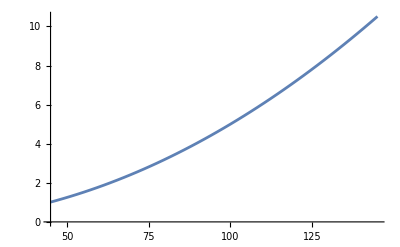

```mathematica
Plot[0.05*0.01 s^2, {s,45,145}]
```

```mathematica
(0.04 - 0.01)*(0.95 - 0.199)*(84 - 16.1)(0.5 - 0.2)*0.5
```

0.229468

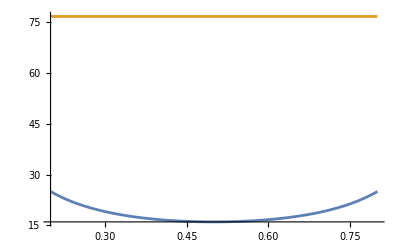

```mathematica
Plot[{4/(z*(1-z)), 0.85*0.01*95^2}, {z,0.2,0.8}]
```

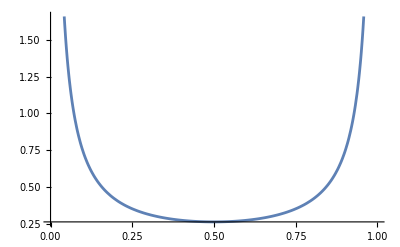

```mathematica
Plot[6/(z*(1-z)*0.01*95^2), {z,0,1}]
```

```mathematica
Integrate[1/(z^2(1-z)^2), {z,a,b},Assumptions->{a>0, b>0}]//FullSimplify
```

ConditionalExpression[1/(-1+a)+1/a+1/(1-b)-1/b+2 Log[((-1+a) b)/(a (-1+b))], 1<a<b]

```mathematica
Integrate[1/(z(1-z)), {z, a, b}, Assumptions->{a>0, b>0}]
```

ConditionalExpression[Log[((-1+a) b)/(a (-1+b))], a<1&&a≠b&&b<1]

```mathematica
Integrate[1/(z*(1-z)),z]
```

-Log[1-z]+Log[z]

```mathematica
r0 = 2;
x0 = 0.01;
s = 95^2;
ymax = 0.9499928204495295;
zmin = 0.200028636082594;
zmax = 0.4999286479605834;
(0.03999798674994404- 0.010013395099609551)Integrate[1, {z, zmin, zmax}, {y, r0^2/(z * (1-z) x0 s), ymax}, {Q2, r0^2/(z*(1-z)), y x0 s}]
```

0.22564